# Iteration Function System (IFS)

## L-System

History

An L-system or Lindenmayer system is a parallel rewriting system and a type of formal grammar. An L-system consists of an alphabet of symbols that can be used to make strings, a collection of production rules that expand each symbol into some larger string of symbols, an initial “axiom” string from which to begin construction, and a mechanism for translating the generated strings into geometric structures. 
L-systems were introduced and developed in 1968 by Aristid Lindenmayer, a Hungarian theoretical biologist and botanist at the University of Utrecht. Lindenmayer used L-systems to describe the behaviour of plant cells and to model the growth processes of plant development. L-systems have also been used to model the morphology of a variety of organisms[1] and can be used to generate self-similar fractals such as iterated function systems.

Definition

A L-system is a formal grammar that understand :
	1. A set of variable alphabet V.
	2. A set of constants values S.
	3. An initital axiom (or seed) to begin W.
	4. A set of rule, noted P
A L-system is noted {V,S,W,P}

Example : Lindenmayer’s seaweed

We considerate the L-système :
V={A,B}
S={}
W=A
P={A→AB,B→A}

When we applied, we obtain :

n=0, A
n=1, AB
n=2, AB A
n=3, AB A AB
n=4, AB A AB AB A
n=5, AB A AB AB A AB A AB

Example : The sequence of Fibonacci

We considerate the L-système  :
V={A,B}
S={}
W=A
P={A→B,B→AB}

When we applied, we obtain :

n=0, A
n=1, B
n=2, AB
n=3, B AB
n=4, AB B AB
n=5, B AB AB B AB

We can counted the symbols number for obtain the sequence of Fibonacci.

n=0, 1 symbol
n=1, 1 symbol
n=2, 2 symbols
n=3, 3 symbols
n=4, 5 symbols
n=5, 8 symbols

Program

We note the program “L-system” with the 4 entries of our L-system and with our iteration “n”.
In output, we will have a list of our L-system language.

```mathematica
Lsystem[V_,S_,W_,P_,n_]:=
{NestList[StringReplace[#,Evaluate[Thread[V->P]]]&,First[W], n]};
```

Dragon curve

In the example of dragon curve, we considerate the L-system :
V={X,Y}
S={A,B}
W={FX}
P={X→WX+YF,Y→-FX-Y}

Here is an example, with the “Dragon” function which takes as input the number of iterations “n”.

```mathematica
Dragon[n_]:=Lsystem[{"X","Y"},{"F","+","-"},{"FX"},{"X+YF+","-FX-Y"},n]
L1=Dragon[5];
M1=Flatten[L1];
M1=Column[M1]//MatrixForm
```

FX
FX+YF+
FX+YF++-FX-YF+
FX+YF++-FX-YF++-FX+YF+--FX-YF+
FX+YF++-FX-YF++-FX+YF+--FX-YF++-FX+YF++-FX-YF+--FX+YF+--FX-YF+
FX+YF++-FX-YF++-FX+YF+--FX-YF++-FX+YF++-FX-YF+--FX+YF+--FX-YF++-FX+YF++-FX-YF++-FX+YF+--FX-YF+--FX+YF++-FX-YF+--FX+YF+--FX-YF+

```mathematica
L1=Last[L1];
```

## Turtle Plot

Definition

In order to use the L-System for represent the IFS, we give a graphical interpretation to each symbols of the alphabet.
This method is called a turtle display or a Turtle Plot.

Program

We will define a simple interpretation :
	 “+“ rotation to the left of a predefined angle lower.
	 “-“ rotation to the right of a lower preset angle.
	 “F” draw a horizontal line of length 1.
	 “X” and “Y” do nothing.
	 “[“ memorizes the current position.
	 “]” returns to last memor position
Here is the programming to define the interpretation.

```mathematica
TMove[{}] = 0.;
TMove[l_List]:=TMove[Last[l]]
TMove[Arrow[{{0.,0.},{l_,0.}}]]:=l
TMove[Line[{{0.,0.},{l_,0.}}]]:=l
TMove[Polygon[{{0.,0.},{_,_},{l_,0.},{_,_},{0.,0.}}]]:=l

Turtle[l_String,tr_,α_:Pi/2.,PlotRange->r_]:=Graphics[First[Fold[Turtle,{{},{{0.,α,0.}}},Characters[l]/.tr]],PlotRange->r]
Turtle[l_String,tr_,α_:Pi/2.]:=Graphics[First[Fold[Turtle,{{},{{0,α,0}}},Characters[l]/.tr]]]
Turtle[{g_,{l___,{x_,y_,a_}}},Angle[b_]]:={g,{l,{x,y,a+b}}}
Turtle[{g_,{l___,h:{x_,y_,a_}}},"["]:={g,{l,h,h}}
Turtle[{g_,{l___,{x_,y_,a_}}},"]"]:={g,{l}}
Turtle[{{g___},{l___,{x_,y_,a_}}},d_List]:=
With[{t=TMove[d]},
{{g,Translate[Rotate[d,a,{0.,0.}],{x,y}]},{l,{x+t Cos[a],y+ t Sin[a],a}}}
]

turtle1=Association[{"F"->{Green,Line[{{0.,0.},{1.,0.}}]},"X"-> {},"Y"->{},"+"-> Angle[90.Degree],"-"-> Angle[-90. Degree]}];
```

Koch curve

The Koch curve is defined from a very simple L-System.
V={F}
S={+,-}
W={F}
P={F→F+F-F-F+F}
Here is the sample display.

```mathematica
Koch[n_]:=Lsystem[{"F"},{"+","-"},{"F"},{"F+F-F-F+F"},n]
Clear[L1];
L1=Koch[10];
M1=Flatten[L1];
M1=Column[M1]//MatrixForm;
L1=Last[L1];
```

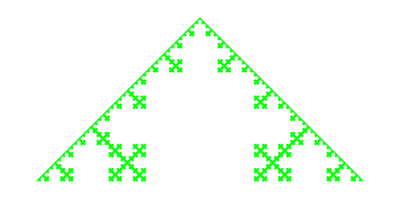

```mathematica
P1=Turtle[L1⟦6⟧,turtle1]
```

Sierpinski Triangle

The Sierpinski triangle has a very simple L-System.
V={A,B}
S={+,-}
W={A}
P={A→B-A-B,B→A+B+A}
We will modify our turtle for it understands A and B the letters used in order to advance.
Morever, the angle must be changed to 60 degrees.

```mathematica
turtle2=Association[{"A"->{Green,Line[{{0.,0.},{1.,0.}}]},"B"->{Green,Line[{{0.,0.},{1.,0.}}]},"+"-> Angle[60.Degree],"-"-> Angle[-60. Degree]}]
```

<|A→{RGBColor[0, 1, 0],Line[{{0.,0.},{1.,0.}}]},B→{RGBColor[0, 1, 0],Line[{{0.,0.},{1.,0.}}]},+→Angle[1.0472],-→Angle[-1.0472]|>

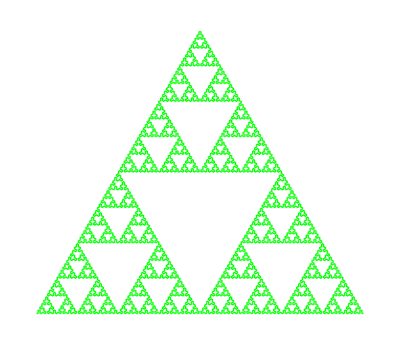

```mathematica
Sierpinski[n_]:=Lsystem[{"A","B"},{"+","-"},{"A"},{"B-A-B","A+B+A"},n]
L2=Sierpinski[10];
M2=Flatten[L2];
M2=Column[M2]//MatrixForm;
L2=Last[L2];
P2=Turtle[L2⟦9⟧,turtle2]
```

Dragon curve

Let’s try to do our turtle on the L-System of our dragon curve with our previous turtle.

```mathematica
turtle3=Association[{"F"->{Green,Line[{{0.,0.},{1.,0.}}]},"X"->{},"Y"->{},"+"->Angle[90.Degree],"-"->Angle[-90. Degree]}]
```

<|F→{RGBColor[0, 1, 0],Line[{{0.,0.},{1.,0.}}]},X→{},Y→{},+→Angle[1.5708],-→Angle[-1.5708]|>

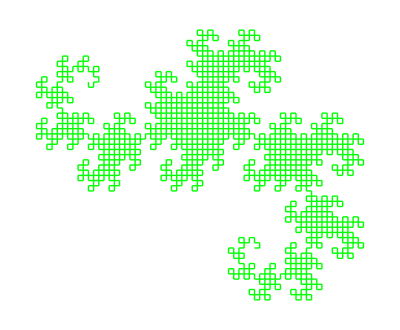

```mathematica
Dragon[n_]:=Lsystem[{"X","Y"},{"F","+","-"},{"FX"},{"X+YF+","-FX-Y"},n]
L3=Dragon[15];
M3=Flatten[L3];
M3=Column[M3]//MatrixForm;
L3=Last[L3];
P3=Turtle[L3⟦12⟧,turtle3]
```

Fractale plant

From an L-System, we go to compute IFS a plant.
However we will change the angle of rotation to 25 degrees.
Here is our L-System:
V={X,F}
S={+,-,[,]}
W={X}
P={X→F-[[X]+X]+F[+FX]-X”,F→FF}

```mathematica
turtle4=Association[{"F"-> {Green,Line[{{0.,0.},{1.,0.}}]},"X"-> {},"Y"-> {},"+"-> Angle[25.Degree],"-"->  Angle[-25. Degree]}]
```

<|F→{RGBColor[0, 1, 0],Line[{{0.,0.},{1.,0.}}]},X→{},Y→{},+→Angle[0.436332],-→Angle[-0.436332]|>

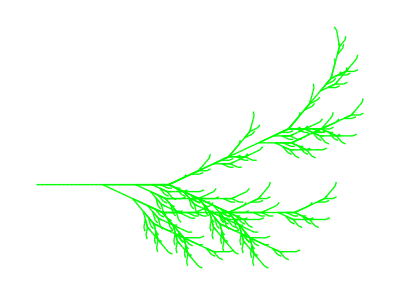

```mathematica
Plante[n_]:=Lsystem[{"X","F"},{"+","-","[","]"},{"X"},{"F-[[X]+X]+F[+FX]-X","FF"},n]
L4=Plante[5];
M4=Flatten[L4];
M4=Column[M4]//MatrixForm;
L4=Last[L4];
P4=Turtle[L4⟦6⟧,turtle4]
```

## Conclusion

```mathematica
DynamicModule[{n=0,P=Graphics[]},Column[{ActionMenu["Precision",{"Faible":>(n=2),"Moyenne":>(n=1),"Haute":>(n=0)}],Dynamic[n];ActionMenu["Fractal",{"Koch Curve":>(P=Turtle[L1⟦6-n⟧,turtle1]),"Sierpinski Triangle ":>(P=Turtle[L2⟦9-n⟧,turtle2]),"Dragon Curve":>(P=Turtle[L3⟦12-n⟧,turtle3]),"Plant":>(P=Turtle[L4⟦6-n⟧,turtle4])}],Dynamic[P]}]]
```